## Plantilla máximos y mínimos

```mathematica
(*programa para máximos y mínimos*)
(*probado con varios ejercicios de internet*)
maxminint[f_,a_,b_]:=Module[{},
d1=D[f,x];
sol=NSolve[D[f,x]==0 && a<x<b,x];
d2=D[f,{x,2}];
d2/.sol;
seg=d2/.sol;

Table[If[seg[[i]]>0,Print["Minimo en x = ",x/.sol[[i]]],
Print["Maximo en =  ",x/.sol[[i]]]],{i,Length[sol]}];
Print[Plot[f,{x,Min[x/.sol]-2,Max[x/.sol]+2}]]
]
```

```mathematica
f=ⅇ^x(x^4-4 x^3+3 x^2+4x-4);
```

Maximo en =  -3.44949

Minimo en x = 0.

Maximo en =  1.44949

Minimo en x = 2.

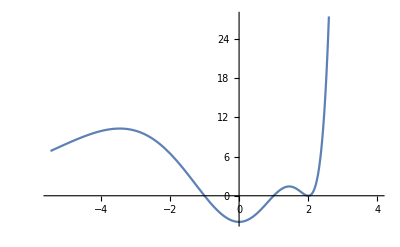

```mathematica
maxminint[f,-∞,∞]
```